## Ireland 2004

## Model Discrepancy

Learning (no mean, no R)

#### Auxiliary Functions I (vectorize by columns, inverse of vectorize by columns)

```mathematica
(*This vectorize is equal to vec(). For vech() we simply use ArrayReshape[].
For the X and Y variables we use vech. For all other we use vec.*)
vectorize[x_,len_]:=ArrayReshape[Transpose[x],{len,1}];

invVectorize[x_,{r_,c_}]:=Transpose[ArrayReshape[x,{c,r}]];
(*We change the order from {r,c} to {c,r}, because the ArrayReshape is by rows instead of by columns. The inverse of vech is ArrayReshape[,{r,c}]. I'll only use ArrayReshape if I want to rebuild an original matrix which was vectorized with vech*)
```

#### Covariance Function

```mathematica
k[ν_,l_,x_,y_]:=Module[{},
(*Esta função dá problemas quando calculada com Norm[x-y]=0... Tem de se fazer o limite, que dá 1.
*)
If [Norm[x-y]==0,
1,
(*2^(1-ν)/Gamma[ν]*(Norm[x-y]*Sqrt[2*ν]/l)^ν*BesselK[ν,Norm[x-y]*Sqrt[2*ν]/l] This is for a general Matern function*)
Exp[-Norm[x-y]/l]
]
];
(*Kint = K_{d1,d2}(X1,X2)*)
Kint[X1_,X2_,l_]:=Module[{},
Table[Table[k[1/2,l,X1⟦i⟧,X2⟦j⟧],{j,1,Length[X2]}],{i,1,Length[X1]}]
(*we're using the rows as vectors. 
In reality, we'll save X in the program as the transpose of the X in the text*)
];
KK[tildeX_,M1_]:=Module[{A},
A=Kint[tildeX,tildeX];
(*ArrayFlatten[Table[Table[A,{i,1,dim}],{j,1,dim}]]
It's faster with the kronecker product*)
KroneckerProduct[M1,A]
]
```

#### RBC Model

```mathematica
rbcACmat[{β_,δ_,θ_,ρ_,aPar_,γ_}]:=Module[{L1,L2,K11,K12,K22,S1,S2,S3,S4,S5,S6,MatPi,W,U,Cmat,CmatStar},

η=1.0051;

L1=(η-β*(1-δ))/(β*η*θ^2);
L2=ρ*(η-β*(1-δ))/(η-β*(1-θ)*(1-δ));
K11=(η-β*(1-θ)*(1-δ))/(β*η*θ);
K12=(β*η*θ^2-η+β*(1-θ^2)*(1-δ))/(β*η*θ^2);
K22=η*θ/(η-β*(1-θ)*(1-δ));
S1=(K22-K11)/K12;
S2=((K22-K11)*L1-K12*L2)/(K12*(K11-ρ));
S3=K22;
S4=K12*L2/(K22-K11)+((K22-ρ)*((K22-K11)*L1-K12*L2))/((K22-K11)*(K11-ρ));
S5={1-(1-θ)/θ*S1,S1+(η/β-1+δ)/(θ^2*(η-1+δ))*(θ-S1),1-1/θ*S1};
S6={1/θ-(1-θ)/θ*S2,S2+(η/β-1+δ)/(θ^2*(η-1+δ))*(1-S2),1/θ-1/θ*S2};

U=Transpose[{Flatten[{S5,S1}],Flatten[{S6,S2}]}];
MatPi={{S3,S4},{0,ρ}};
(*W={{0},{1}};*)

ysteady=aPar^(1/(1-θ))*(θ/(η/β-1+δ))^(θ/(1-θ))*(1-θ)/γ*(1-θ*(η-1+δ)/(η/β-1+δ))^-1;

csteady=(1-θ*(η-1+δ)/(η/β-1+δ))*ysteady;

hstead=(1-θ)/γ*(1-θ*(η-1+δ)/(η/β-1+δ))^-1;


Cmat=Drop[U,{2}];
CmatStar={{Log[ysteady]},{Log[hstead]},{Log[csteady]}};

{MatPi,Cmat,CmatStar}
]
```

#### Auxiliary Functions II (reparametrizations, sparse matrices, etc)

Some functions will not be used in the final simulations, namely those that build the matrix derivatives. Check the Appendix on the Phd - Thesis. However, I' ve decided to keep them for completeness.

```mathematica
(**)

spmatSigma[T_,dim_]:=Module[{},
idT=IdentityMatrix[T,SparseArray];
idDim=IdentityMatrix[dim,SparseArray];
KroneckerProduct[Flatten[Table[KroneckerProduct[idDim,Transpose[{idT[[i]]}]],{i,1,T}],1],idDim]];

spmatL[M1_,T_]:=Module[{},
KroneckerProduct[IdentityMatrix[T,SparseArray],Flatten[Table[KroneckerProduct[IdentityMatrix[T,SparseArray],Transpose[{M1[[;;,i]]}]],{i,1,Length[M1]}],1]]];

funcHM[KM_,dim_,T_]:=Module[{},
KroneckerProduct[Flatten[Table[KroneckerProduct[IdentityMatrix[dim,SparseArray],Transpose[{KM[[;;,i]]}]],{i,T}],1],IdentityMatrix[dim,SparseArray]]
];

logit[u_]:=Module[{x},
x=SetPrecision[u,50];
Log[x/(1-x)]
];
(*melhorar a precisão do cálculo nestas funções*)

invLogit[u_]:=Module[{x},x=SetPrecision[u,50];E^x/(1+E^x)];

linTanTransf[u_]:=Module[{x},
x=SetPrecision[u,50];
Tan[x*Pi/2]
];

invLinTanTransf[u_]:=Module[{x},
x=SetPrecision[u,50];
ArcTan[x]/(Pi/2)];

reparametrizationMatern[L_]:=Log[L];
reparametrizationMaternInv[tilL_]:=Exp[tilL];

reparametrizationF[{β_,δ_,θ_,ρ_,aPar_,γ_}]:=Module[{},
{logit[β],logit[δ],logit[θ],logit[ρ],Log[aPar],Log[γ]}
];(*Transforms original thetas into tilde thetas*)

reparametrizationFInv[{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_}]:=Module[{},
{invLogit[tilβ],invLogit[tilδ],invLogit[tilθ],invLogit[tilρ],Exp[tilaPar],Exp[tilγ]}
];(*Transforms tilde thetas into original thetas*)

reparametrizationFQS[{Q_,Sigma_}]:=Module[{},

If[Dimensions[Q]=={2,2},
{DiagonalMatrix[Log[Diagonal[Q]]],
DiagonalMatrix[Log[Diagonal[Sigma]]]},
{Log[Q],Log[Sigma]}
]
];(*Transforms Q and Sigma into tilde Q and Sigma. Works either with main diagonals or the whole matrices.*)

reparametrizationFQSInv[{tilQ_,tilSigma_}]:=Module[{},
If[Dimensions[tilQ]=={2,2},
{DiagonalMatrix[E^Diagonal[tilQ]],
DiagonalMatrix[E^Diagonal[tilSigma]]},
{E^tilQ,E^tilSigma}
]
];

(*Transforms tilde Q and Sigma into original Q and Sigma. Works both with just the main diagonal or the whole matrices*)

{Astruct,Cmatstruct,CmatStarstruct}=rbcACmat[reparametrizationFInv[{ntilβ,ntilδ,ntilθ,ntilρ,ntilaPar,ntilγ}]];
(*A,Cmat e CmatStar são reparametrizados à custa dos til economic parameters*)
(*Usar FullImplify  para simplificar fórmulas e serem mais rápidas a calcular.*)

derAstruct[{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_}]:=Table[D[Astruct[[i,j]], {{ntilβ,ntilδ,ntilθ,ntilρ,ntilaPar,ntilγ}}],{i,1,2},{j,1,2}]/.{ntilβ->tilβ,ntilδ->tilδ,ntilθ->tilθ,ntilρ->tilρ,ntilaPar->tilaPar,ntilγ->tilγ};
(*Derivamos A em relação aos parâmetros tilde theta*)

derCmatstruct[{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_}]:=Table[D[Cmatstruct[[i,j]], {{ntilβ,ntilδ,ntilθ,ntilρ,ntilaPar,ntilγ}}],{i,1,3},{j,1,2}]/.{ntilβ->tilβ,ntilδ->tilδ,ntilθ->tilθ,ntilρ->tilρ,ntilaPar->tilaPar,ntilγ->tilγ};
(*Derivamos Cmat em relação aos parâmetros tilde theta*)

derCmatStarstruct[{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_}]:=Table[D[CmatStarstruct[[i,j]], {{ntilβ,ntilδ,ntilθ,ntilρ,ntilaPar,ntilγ}}],{i,1,3},{j,1,1}]/.{ntilβ->tilβ,ntilδ->tilδ,ntilθ->tilθ,ntilρ->tilρ,ntilaPar->tilaPar,ntilγ->tilγ};
(*Derivamos CmatStar em relação aos parâmetros tilde theta*)

derKM[X1T_,tilL_]:=Module[{},
Table[
Table[k[1/2,Exp[tilL],X1T⟦i⟧,X1T⟦j⟧]*Norm[X1T⟦i⟧-X1T⟦j⟧]*Exp[-tilL],
{j,1,Length[X1T]}],
{i,1,Length[X1T]}]
];

upperTriangular[v_,n_]:=Module[{i=0,j=0},
Array[If[#>#2,0,v[[++i]]]&,{n,n}]
];(*To create an upper triangular matrix from a vector. We shall use this in drawProp for M1 matrix*)
```

#### Auxiliary Functions III (Normal density,positivizeMatrix, etc)

```mathematica
(*transitionDrawPG and condNormal will be used in the PGASMK algorithm*)

transitionDrawPG[xt1_,A_,Q_]:=RandomVariate[MultinormalDistribution[Flatten[A.xt1],Q]];


positivizeMatrix[X_]:=Module[{res},

res=X;

res=0.5*(res+Transpose[res]);
(*This method only works for Hermitian matrices*)

If[Not[PositiveDefiniteMatrixQ[res]]||MatrixRank[res]≠Length[res],

auxsystDP=Eigensystem[res];

duDP=DiagonalMatrix[auxsystDP[[1]]];

wDP=ReplacePart[duDP,{i_,i_}/;duDP[[i,i]]≤0:>0];

lenRes=Length[res];

powerDP=30;

While[Not[PositiveDefiniteMatrixQ[res]]||MatrixRank[res]≠Length[res],

res=Transpose[auxsystDP[[2]]].(wDP+IdentityMatrix[lenRes]*$MinMachineNumber*2^(-powerDP)).auxsystDP[[2]];

res=0.5*(res+Transpose[res]);
(*Machine Precision considerations make the above mandatory! Not theoretically needed.*)

powerDP--;
]; 
];
res
];

logMultinormalDens[x_,mean_,var2_]:=Module[{t,det,var},
(*Theoretically, I've made sure var2 is PD and Sym, however, due to machine-precision considerations, we must make sure it's symmetric. Otherwise we would have an error warning from mathematica*)

var=positivizeMatrix[var2];

t=Quiet[0.5*(x-mean).LinearSolve[var,(x-mean),Method->"Cholesky"]];

det=(2*Pi)^Length[var]*Det[var]^(0.5);

-t-Log[det]
];

logCondNormal[vecy1T_,X1T_,t1_,t2_,M1PG_,tilL_,CmatPG_,CmatStarPG_,SigmaPG_]:=Module[{}, 
(*{fvecy1T,vecy1tminus1,vecytT,mean,mean1tminus1,meantT,varMat,varMatTT,varMat1t,varMat1tT,meancond,varcond,fvy}*)

(*N(y1|y2) com dim(y1)=3*t1 e dim(y1)+dim(y2)=3*t2 *)

(*vecy1T tem de ser flattened*)
fvecy1T=Flatten[vecy1T];

vecy1tminus1=fvecy1T[[1;;3*t1]];(*(t1-1)*)

vecytT =fvecy1T[[3*t1+1;;3*t2]];

mean=Flatten[KroneckerProduct[IdentityMatrix[t2],CmatPG].ArrayReshape[X1T,{2*t2,1}]+KroneckerProduct[ConstantArray[1,t2],IdentityMatrix[3]].CmatStarPG];
(*We must use ArrayReshape, since X1T was made using observations as ROWS, Not columns*)

mean1tminus1=mean[[1;;3*t1]];

meantT=mean[[3*t1+1;;]];

X1t2=X1T[[1;;t2]];

varMat=positivizeMatrix[KroneckerProduct[Kint[X1t2,X1t2,Exp[tilL]],M1PG]+KroneckerProduct[IdentityMatrix[t2],SigmaPG]];

varMatTT=varMat[[3*t1+1;;,3*t1+1;;]];

varMat1t=varMat[[1;;3*t1,1;;3*t1]];

varMat1tT=varMat[[1;;3*t1,3*t1+1;;]];


meancond=Quiet[Flatten[meantT+Transpose[varMat1tT]. LinearSolve[varMat1t,(vecy1tminus1-mean1tminus1)]]];

varcond= Quiet[varMatTT-Transpose[varMat1tT]. LinearSolve[varMat1t,varMat1tT]];


(*Theoretically the next lines of code shouldn't be needed, but due to numerical machine accuracy, we sometimes need this*)

varcond=positivizeMatrix[varcond];

t=Quiet[0.5*(vecytT-meancond).LinearSolve[varcond,(vecytT-meancond),Method->"Cholesky"]];
(*Quiet quiets non-critical warnings, like numerically unstable matrices. *)

det=(2*Pi)^Length[varcond]*Det[varcond]^(0.5);
(*Theoretically the above line of code shouldn't need Abs, but due to numerical machine accuracy, we sometimes need this*)

-t-Log[det]

];
```

#### Mean for Econ

```mathematica
newMeanEcon[vecy1T_,vecx2T_,vecx1T1_,vecx1T_,X1T_,T_,KM_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_]:=Module[{},

Tilparam={tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}+s1*RandomReal[{-1,1},6];

Tilparam

];
```

#### Mean for Vars

```mathematica
newMeanVars[vecy1T_,vecx2T_,vecx1T1_,vecx1T_,X1T_,T_,KM_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_]:=Module[{},

resTilVars={tilQMat+s1*DiagonalMatrix[RandomReal[{-1,1},2]],tilSigmaMat+s1*DiagonalMatrix[RandomReal[{-1,1},3]]};
resTilVars

];
```

#### Mean for tilL

```mathematica
newMeanL[vecy1T_,vecx2T_,vecx1T1_,vecx1T_,X1T_,T_,KM_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_]:=Module[{},

newtiL=tilL+s1*RandomReal[{-1,1}];

newtiL

];
```

#### Mean for M1(in the proposal we adjust for the d.f.)

```mathematica
newMeanM1[vecy1T_,vecx2T_,vecx1T1_,vecx1T_,X1T_,T_,KM_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_]:=Module[{},

CovMat=IdentityMatrix[3];(*RandomVariate[InverseWishartMatrixDistribution[3,IdentityMatrix[3]]];*)

newM1=M1+s1*s1M1*RandomVariate[InverseWishartMatrixDistribution[nuM1,CovMat]];

newM1

];
```

#### Marginal Likelihood

```mathematica
logMarginalLikelihood[vecy1T_,X1T_,T_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}}]:=Module[{},

vecx1TLik=ArrayReshape[X1T,{Times@@Dimensions[X1T],1}];
(*We must use ArrayReshape since X1T is has in each ROW an observation*)

{ALik,CmatLik,CmatStarLik}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QLik,SigmaLik}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];


If[T==1,
KMLik={{1}};
resLik=logMultinormalDens[X1T[[1]],{0,0},IdentityMatrix[2]]+logMultinormalDens[Flatten[vecy1T],Flatten[KroneckerProduct[IdentityMatrix[T],CmatLik].Flatten[vecx1TLik]+KroneckerProduct[ConstantArray[1,T],IdentityMatrix[3]].CmatStarLik],KroneckerProduct[KMLik,M1]+KroneckerProduct[IdentityMatrix[T],SigmaLik]]
];


If[T≥2,
x2TLik=Drop[X1T,1];

x1T1Lik=Drop[X1T,-1];

(*We must use ArrayReshape since X1T  has in each ROW an observation*)
vecx2TLik=ArrayReshape[x2TLik,{Times@@Dimensions[x2TLik],1}];

vecx1T1Lik=ArrayReshape[x1T1Lik,{Times@@Dimensions[x1T1Lik],1}];

KMLik=Kint[X1T,X1T,Exp[tilL]];

resLik=logMultinormalDens[X1T[[1]],{0,0},IdentityMatrix[2]]+logMultinormalDens[Flatten[vecx2TLik],Flatten[(KroneckerProduct[IdentityMatrix[T-1],ALik].vecx1T1Lik)],KroneckerProduct[IdentityMatrix[T-1],QLik]]+logMultinormalDens[Flatten[vecy1T],Flatten[KroneckerProduct[IdentityMatrix[T],CmatLik].vecx1TLik+KroneckerProduct[ConstantArray[1,T],IdentityMatrix[3]].CmatStarLik],KroneckerProduct[KMLik,M1]+KroneckerProduct[IdentityMatrix[T],SigmaLik]];

];
resLik
];
```

#### Prior(Options for M1: Chang Eaves, Wishart, Inv-Wishart)

```mathematica
(*Define multivariate gamma for the density of Inverse Wishart*)multiΓ[p_,a_]:=π^(p*(p-1)/4) Product[Gamma[a+(1-j)/2],{j,1,p}]
```

```mathematica
(*Density function of inverse Wishart*)
logDensInvWish[Σ_,ν_,X2_]:=Module[{len,eigen,lbnugget,cond,logpropconst},

(*ν must be greater than number of lines/columns of Σ *)

(*machine-precision considerations*)

len=Length[Σ];

Xdens=0.5*(X2+Transpose[X2]);

cond=0.5*Tr[Σ.Inverse[Xdens]];

logpropconst=Log[Abs[Det[Σ]]^(ν/2)]-Log[(2^(ν*len/2)*multiΓ[len,ν/2])]+Log[Norm[Det[Xdens]]^(-(ν+len+1)/2)] ;

(*If[-cond+Log[propconst]<10. Log[$MinMachineNumber],
0(*We need this, otherwise we'll have underflow problems, coming from Exp[-cond]*),
propconst*Exp[-cond]
]*)

-cond+logpropconst
];
```

```mathematica
(*Kernel density for Chang and Eaves 's Objective Prior*)
logChangEaves[X_]:=Module[{len,cond,eigen,lbnugget},
len=Length[X];
Xdens=0.5*(X+Transpose[X]);

Log[Norm[Det[Xdens]]^(-0.5*(len+1))]+Log[Norm[Det[IdentityMatrix[len]+Xdens*Inverse[Xdens]]]^(-0.5)]

(*The density is PROPORTIONAL to the result*)
];


absDetJacob[{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}]:=Module[{},
Abs[E^tilβ/(1+E^tilβ)^2*E^tilδ/(1+E^tilδ)^2*E^tilθ/(1+E^tilθ)^2*E^tilρ/(1+E^tilρ)^2*Exp[tilaPar+tilγ+tilL]*Apply[Times, E^Diagonal[tilQMat]]*Apply[Times,E^Diagonal[tilSigmaMat]]
]
];(*Absolute Value of Jacobian's Determinant*)


logPriorTheta[{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}}]:=Module[{},

{βprior,δprior,θprior,ρprior,aParprior,γprior}=reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}];

{Qprior,Sigmaprior}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];


(*If a rho draw is negative, then we'll get a zero from the prior.*)
Log[
PDF[BetaDistribution[9.9,1.7],βprior]*PDF[BetaDistribution[1,10],δprior]*PDF[BetaDistribution[5,10],θprior]*PDF[BetaDistribution[9.9,1.7],ρprior]*PDF[GammaDistribution[10,0.5],aParprior]*PDF[GammaDistribution[0.25,0.1],γprior]*PDF[GammaDistribution[2,2],Exp[tilL]]*PDF[InverseGammaDistribution[2.5,0.5],Qprior[[1,1]]]*PDF[InverseGammaDistribution[2.5,0.5],Qprior[[2,2]]]*PDF[InverseGammaDistribution[2.5,0.5],Sigmaprior[[1,1]]]*PDF[InverseGammaDistribution[2.5,0.5],Sigmaprior[[2,2]]]*PDF[InverseGammaDistribution[2.5,0.5],Sigmaprior[[3,3]]]*absDetJacob[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}]
]+logDensInvWish[IdentityMatrix[3],15,M1]

];
```

#### Draws for Proposals and Pdfs

```mathematica
drawPropEcon[mean_,s2_]:=Module[{draw},

scaleMatrixEcon=IdentityMatrix[6];

(*If[Select[mean,Element[#,Reals]&]≠mean,
mean2={tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ};
,
mean2=mean;
];*)
(*scaleMatrixEcon[[4,4]]=5;*)

draw=RandomVariate[MultivariateTDistribution[mean,s2*scaleMatrixEcon,3]];

draw

];

pdfPropEcon[x_,mean_,s2_]:=Module[{pdf},

pdf=PDF[MultivariateTDistribution[mean,s2*scaleMatrixEcon,3],x];

(*Check[pdf=PDF[MultivariateTDistribution[mean,s2*scaleMatrixEcon,3],x],
Print["x = ", InputForm[x]];
Print["mean = ", InputForm[mean]];
pdf=PDF[MultivariateTDistribution[mean,s2*scaleMatrixEcon,3],x]
];*)

pdf
];
```

```mathematica
drawPropVars[{meanQ_,meanSigma_},s2_]:=Module[{},

scaleMatrixVars=IdentityMatrix[5];


mean=Flatten[{Diagonal[meanQ],Diagonal[meanSigma]}];

tSampleDP=RandomVariate[MultivariateTDistribution[mean,s2*scaleMatrixVars,3]];


newtilQDP=DiagonalMatrix[tSampleDP[[1;;2]]];

newtilSigmaDP=DiagonalMatrix[tSampleDP[[3;;5]]];

{newtilQDP,newtilSigmaDP}
(*drawProp outputs the tilde parameters for the economic structural parameters, and also tilde Q and tilde Sigma.
Everything as matrices, except resnewstruc which goes out as a vector, and resnewLgp as a number*)

];

pdfPropVars[{xQ_,xSigma_},{meanQ_,meanSigma_},s2_]:=Module[{pdf},

pdf=PDF[MultivariateTDistribution[Flatten[{Diagonal[meanQ],Diagonal[meanSigma]}],s2*scaleMatrixVars,3],Flatten[{Diagonal[xQ],Diagonal[xSigma]}]];

pdf
];
```

```mathematica
drawPropL[mean_,s2_]:=Module[{},
RandomVariate[StudentTDistribution[mean,s2,3]]
];

pdfPropL[x_,mean_,s2_]:=Module[{},
PDF[StudentTDistribution[mean,s2,3],x]
];
```

```mathematica
drawPropM1[mean_,s2_]:=Module[{},

(*nu=5;*)

matrixM1Prop=(*mean;*)positivizeMatrix[mean*(nuM1+Length[mean]+1)];
(*We need this, since sometimes multiplying by nu+Length[mean]+1 will return a non-SPD matrix due to machine precision considerations...*)

RandomVariate[InverseWishartMatrixDistribution[nuM1,matrixM1Prop]]

];

logPdfPropM1[x_,mean_,s2_]:=Module[{},
(*nu=5;*)
logDensInvWish[mean*(nuM1+Length[mean]+1),nuM1,x]
]
```

#### Auxiliary Functions 4 (Acceptance Step for MH Steps)

```mathematica
AcceptanceStep[vecy1T_,X1T_,T_,thetaMinusList_,thetaStarList_,newMeanGivenThetaMinus1_,newMeanGivenThetaStarList_,s1_,s2_,option_]:=Module[{},

(*thetaMinusList={{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,tilQMat};
*)

(* option==1, Econ Step
 option==2, L Step
 option==3, Q,Sigma Step 
 option==4, M1 step *)

logdenominatorprior=logPriorTheta[thetaMinusList];

logdenominatorproposal=Which[option==1,Log[pdfPropEcon[thetaStarList[[2]],newMeanGivenThetaMinus1,s2]],
option==2,Log[pdfPropL[thetaStarList[[3]],newMeanGivenThetaMinus1,s2]],
option==3,Log[pdfPropVars[thetaStarList[[4]],newMeanGivenThetaMinus1,s2]],
option==4,logPdfPropM1[thetaStarList[[1]],newMeanGivenThetaMinus1,s2]
];


(*thetaStarList={M1,drawPropEcon[newMeanEconGivenThetaMinus1,s2],tilL,{tilQMat,tilSigmaMat}};*)

logdenominatorlikelihood=logMarginalLikelihood[vecy1T,X1T,T,thetaMinusList];

logdenominator=logdenominatorprior+logdenominatorproposal+logdenominatorlikelihood;

(*--- Numerator ---*)

lognumeratorprior=logPriorTheta[thetaStarList];

lognumeratorlik=logMarginalLikelihood[vecy1T,X1T,T,thetaStarList];

lognumeratorproposal=Which[option==1,Log[pdfPropEcon[thetaMinusList[[2]],newMeanGivenThetaStarList,s2]],
option==2,Log[pdfPropL[thetaMinusList[[3]],newMeanGivenThetaStarList,s2]],
option==3,Log[pdfPropVars[thetaMinusList[[4]],newMeanGivenThetaStarList,s2]],
option==4,
logPdfPropM1[thetaMinusList[[1]],newMeanGivenThetaStarList,s2]
];

(*thetaStarList={M1,drawPropEcon[newMeanEconGivenThetaMinus1,s2],tilL,{tilQMat,tilSigmaMat}};*)

logAcceptprob=Min[{0,(lognumeratorprior+lognumeratorproposal+lognumeratorlik-logdenominator)}
];
(*Log[1]=0*)

u=RandomVariate[UniformDistribution[{0,1}],1][[1]];

If[Log[u]≤ logAcceptprob,

res=thetaStarList;

counterMH=1;,

counterMH=0;

res=thetaMinusList;  
];

{res,counterMH}

];
```

#### M-H step Econ

```mathematica
MHstepEcon[vecy1T_,X1T_,T_,dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_,s2_]:=Module[{},

(*Print[" - - Entrando no MH - - "];
*)

(*x2TMH=Drop[X1T,1];

x1T1MH=Drop[X1T,-1];

(*We use ArrayReshape since the matrix X1T is made of ROWS of observations*)

vecx2TMH=ArrayReshape[x2TMH,{Times@@Dimensions[x2TMH],1}];

vecx1TMH=ArrayReshape[X1T,{Times@@Dimensions[X1T],1}];

vecx1T1MH=ArrayReshape[x1T1MH,{Times@@Dimensions[x1T1MH],1}];*)

(*The Vectorizations above will be in the MHGlobal to be more efficient.*)


KMMH=Kint[X1T,X1T,Exp[tilL]];


{AMH,CmatMH,CmatStarMH}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QMH,SigmaMH}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];

thetaMinusList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};

newMeanEconGivenThetaMinus1=newMeanEcon[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMH,{M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}},s1];
(* mean for q(θ_* | θ[n-1], X1:T, y1:T) *)

thetaStarList={M1,drawPropEcon[newMeanEconGivenThetaMinus1,s2],tilL,{tilQMat,tilSigmaMat}};
(*thetastarlist is the candidate theta draw as a list of lists. We'll need to transform it into a proper vector using only the upper triangular matrix of M1, the main diagonal of Q and Sigma*)


KMMHThetaStar=KMMH;
(*In this MH step, KMMH = Kint[X1T,X1T,Exp[thetaStarList⟦3⟧]]; *)


newMeanEconGivenThetaStarList=newMeanEcon[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMHThetaStar,thetaStarList,s1];
(* mean for q(θ[n-1]|θ_* , X1:T, y1:T) *)


(*thetaStar is the theta_* vector which will enter in the proposal density*)

AcceptanceStep[vecy1T,X1T,T,thetaMinusList,thetaStarList,newMeanEconGivenThetaMinus1,newMeanEconGivenThetaStarList,s1,s2,1]
(*AcceptanceStep[vecy1T_,X1T_,T_,thetaMinusList_,thetaStarList_,newMeanGivenThetaMinus1_,newMeanGivenThetaStarList_,s1_,s2_,option_]*)
];
```

#### M-H Step L

```mathematica
MHstepL[vecy1T_,X1T_,T_,dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_,s2_]:=Module[{},


KMMH=Kint[X1T,X1T,Exp[tilL]];


{AMH,CmatMH,CmatStarMH}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QMH,SigmaMH}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];

thetaMinusList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};

newMeanLGivenThetaMinus1=newMeanL[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMH,{M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}},s1];
(* mean for q(θ_* | θ[n-1], X1:T, y1:T) *)

thetaStarList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},drawPropL[newMeanLGivenThetaMinus1,s2],{tilQMat,tilSigmaMat}};
(*thetastarlist is the candidate theta draw as a list of lists. We'll need to transform it into a proper vector using only the upper triangular matrix of M1, the main diagonal of Q and Sigma*)


KMMHThetaStar=Kint[X1T,X1T,Exp[thetaStarList⟦3⟧]];
(*In this MH step KMMH is different, because thetaStarList⟦3⟧ is different from tilL*)


newMeanLGivenThetaStarList=newMeanL[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMHThetaStar,thetaStarList,s1];
(* mean for q(θ[n-1]|θ_* , X1:T, y1:T) *)

AcceptanceStep[vecy1T,X1T,T,thetaMinusList,thetaStarList,newMeanLGivenThetaMinus1,newMeanLGivenThetaStarList,s1,s2,2]

];
```

#### M-H Step Vars

```mathematica
MHstepVars[vecy1T_,X1T_,T_,dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_,s2_]:=Module[{},

KMMH=Kint[X1T,X1T,Exp[tilL]];


{AMH,CmatMH,CmatStarMH}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QMH,SigmaMH}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];

thetaMinusList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};

newMeanVarsGivenThetaMinus1=newMeanVars[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMH,{M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}},s1];
(* mean for q(θ_* | θ[n-1], X1:T, y1:T) *)

thetaStarList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,drawPropVars[newMeanVarsGivenThetaMinus1,s2]};
(*thetastarlist is the candidate theta draw as a list of lists. We'll need to transform it into a proper vector using only the upper triangular matrix of M1, the main diagonal of Q and Sigma*)

(*Print["2"];*)

KMMHThetaStar=KMMH;
(*In this MH step, KMMH = Kint[X1T,X1T,Exp[thetaStarList⟦3⟧]]; *)

newMeanVarsGivenThetaStarList=newMeanVars[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMHThetaStar,thetaStarList,s1];
(* mean for q(θ[n-1]|θ_* , X1:T, y1:T) *)
(*Print["3"];*)

AcceptanceStep[vecy1T,X1T,T,thetaMinusList,thetaStarList,newMeanVarsGivenThetaMinus1,newMeanVarsGivenThetaStarList,s1,s2,3]


];
```

#### M-H Step M1

```mathematica
MHstepM1[vecy1T_,X1T_,T_,dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_,s2_]:=Module[{},

KMMH=Kint[X1T,X1T,Exp[tilL]];


{AMH,CmatMH,CmatStarMH}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QMH,SigmaMH}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];

thetaMinusList={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};

newMeanM1GivenThetaMinus1=newMeanM1[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMH,{M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}},s1];
(* mean for q(θ_* | θ[n-1], X1:T, y1:T) *)

(*Print[1];*)

thetaStarList={drawPropM1[newMeanM1GivenThetaMinus1,s2],{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};
(*thetastarlist is the candidate theta draw as a list of lists. We'll need to transform it into a proper vector using only the upper triangular matrix of M1, the main diagonal of Q and Sigma*)
(*Print[2];*)

KMMHThetaStar=KMMH;
(*In this MH step KMMH = Kint[X1T,X1T,Exp[thetaStarList⟦3⟧]]*)


newMeanM1GivenThetaStarList=newMeanM1[vecy1T,vecx2TMH,vecx1T1MH,vecx1TMH,X1T,T,KMMHThetaStar,thetaStarList,s1];
(* mean for q(θ[n-1]|θ_* , X1:T, y1:T) *)

(*Print["Before acceptstep"];*)
AcceptanceStep[vecy1T,X1T,T,thetaMinusList,thetaStarList,newMeanM1GivenThetaMinus1,newMeanM1GivenThetaStarList,s1,s2,4]

];
```

#### M-H Global

```mathematica
MHstepGlobal[vecy1T_,X1T_,T_,dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},s1_,s2_]:=Module[{},


x2TMH=Drop[X1T,1];

x1T1MH=Drop[X1T,-1];

(*We use ArrayReshape since the matrix X1T is made of ROWS of observations*)

vecx2TMH=ArrayReshape[x2TMH,{Times@@Dimensions[x2TMH],1}];

vecx1TMH=ArrayReshape[X1T,{Times@@Dimensions[X1T],1}];

vecx1T1MH=ArrayReshape[x1T1MH,{Times@@Dimensions[x1T1MH],1}];

(*The vectorizations above will be used by all the MH Steps defined above.*)

(*Print["MHstepEcon"];*)
{resGlobal,acceptEcon}=MHstepEcon[vecy1T,X1T,T,dim,{M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}},s1,s2];

(*Print["MHstepVars"];*)
{resGlobal,acceptVars}=MHstepVars[vecy1T,X1T,T,dim,resGlobal,s1,s2];

(*Print["MHstepL"];*)
{resGlobal,acceptL}=MHstepL[vecy1T,X1T,T,dim,resGlobal,s1,s2];

(*Print["MHstepM1"];*)
{resGlobal,acceptM1}=MHstepM1[vecy1T,X1T,T,dim,resGlobal,s1,s2];

{resGlobal,{acceptEcon,acceptVars,acceptL,acceptM1}}

];
```

#### PGASMK (Parallelized)

```mathematica
(*Particle Gibbs Ancestor Sampling Markov Kernel*)

PGASMK[vecy1T_,X1T_,numParticles_,T_, dim_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}}]:=Module[{},

{APG,CmatPG,CmatStarPG}=rbcACmat[reparametrizationFInv[{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ}]];

{QPG,SigmaPG}=reparametrizationFQSInv[{tilQMat,tilSigmaMat}];

M1PG=M1;

refX1TPG=X1T;
(*with dimensions T*2  *)

partmatXPG=ConstantArray[0,{T,numParticles}];(*each line t, with row i, will have a x_{t}^i. See step 7*)

matX1tPG=ConstantArray[0,{numParticles}];

normWlistPG=ConstantArray[0,T];

ancmatPG=ConstantArray[0,{T,numParticles}];(*ancmat is the matrix where each column will give the history for each particle.
Column i, is the whole ancestry of particle i, up to time t, i.e. {1,a^i_1} to {t,a^i_{t}}
The first line will have only zeros, since x_1 has no ancestors*)

partmatXPG[[1]]=RandomVariate[MultinormalDistribution[{0,0},2*IdentityMatrix[2]],numParticles];
(*each line t, with row i, will have a x_{t}^i*)
(*supposedly we only need up to num-1, but it's faster this way
Also, partmatX[[1]] is x_0*)

matX1tPG=Transpose[{partmatXPG[[1]]}];
(*This is step 2*)

partmatXPG[[1,numParticles]]=refX1TPG[[1]];

matX1tPG[[numParticles,1]]=refX1TPG[[1]];
(*this is step 3*)

normWPG=ConstantArray[1/numParticles,numParticles];

columnlistPG=Table[i,{i,1,numParticles}];(*n.ba of columns in vector for partmatX, or ancmat*)

timePG=2;(* time=1 é tempo 0 para partmatX*)

While[timePG≤T(*T*),


normWlistPG[[timePG-1]]=normWPG;

(*Print["normWlistPG=",normWlistPG];*)

aitPG=Position[RandomVariate[MultinomialDistribution[1,normWPG],numParticles],1][[;;,2]];(*ait is a vector of categories, stating where each comes from, i.e. it's a_t^i*)
(*This is step 6*)

(*Print["2"];*)

ait2PG=Transpose[{ConstantArray[timePG-1,numParticles],aitPG}];
(*vector with elements ait2[[i]]={(t-1)-th time, a_t^i}*)

ancmatPG[[timePG]]=ait2PG;(*ancestry for time = timePG*)

xt1aitPG=Extract[partmatXPG,ait2PG];
(*This creates x_{t-1}^{a_t^i}, which is the only value need for step 7*)

(*Print["3"];*)

partmatXPG[[timePG]]=ParallelMap[transitionDrawPG[#,APG,QPG]&,xt1aitPG];
(*This is step 7.
It's faster to do for every column. Last column will be changed below.*)

partmatXPG[[timePG,numParticles]]=refX1TPG[[timePG]];
(*This is step 10. Its order is interchangeable, as long as it's computed before normW*)


(*Print["4"];*)

matX1TrefX1TPG=Parallelize[Map[Join[matX1tPG[[#]],refX1TPG[[timePG;;T]]]&,columnlistPG]];
(*At the least, we always use x_1.
matX1TrefX1TPG is a matrix in which each i-th ROW has (x_{1:t-1}^i,\tilde{x}_{t:T}).
We need this for tilde weights*)

(*Print["5"];*)

normWPG=(normWPG/.{0.->$MinMachineNumber});
(*So that we can use Log[]. If the other elements are very different, when we normalize tildeWPG, they will have a negligible effect*)

tildeWPG=Log[normWPG]+Parallelize[MapThread[logMultinormalDens[refX1TPG[[timePG]],APG.(#2[[timePG-1]]),QPG]+logCondNormal[vecy1T,#1,timePG-1,T,M1PG,tilL,CmatPG,CmatStarPG,SigmaPG]&,{matX1TrefX1TPG,matX1tPG}]];

(*multinormalDens[x_,mean_,var2_]*)

min=Min[tildeWPG];
(*Print["6"];*)

tildeWPG=Exp[tildeWPG-min];

tildeWPG=tildeWPG/.{Indeterminate->1,Underflow[]->$MinMachineNumber,Overflow[]->$MaxMachineNumber};

tildeWPG=Normalize[Threshold[Normalize[tildeWPG,Total],$MachineEpsilon/10],Total];
(*We need Threshold, because when there's path degeneracy, we get non-machine level numbers in the normalization s*)

If[Select[tildeWPG,(#===Indeterminate||#===Underflow[]||#===Overflow[])&]≠{}||Total[tildeWPG]≠1,tildeWPG=ConstantArray[1/numParticles,numParticles];
Print["tildeWPG is constant"];
];


ancmatPG[[timePG,numParticles]]={timePG-1,Position[RandomVariate[MultinomialDistribution[1,tildeWPG],1],1][[;;,2]][[1]]};

(*Print["7"];*)

matX1tPG=ParallelTable[
Join[matX1tPG[[ancmatPG⟦timePG,i,2⟧]],{partmatXPG[[timePG,i]]}],{i,1,numParticles}];

(*This is step 11. 
Each i-th ROW has (x_{1:t-1}^{a_i},x_t^i)=x^i_{1:t} *)

(*Print["8"];*)

normWPG=ParallelMap[(logCondNormal[vecy1T,matX1tPG[[#]],timePG-1,timePG,M1PG,tilL,CmatPG,CmatStarPG,SigmaPG])&,Table[i,{i,1,numParticles}]];

min2=Min[normWPG];

normWPG=Exp[normWPG-min2];

normWPG=normWPG/.{Indeterminate->1,Underflow[]->$MinMachineNumber,Overflow[]->$MaxMachineNumber};

normWPG=Normalize[Threshold[Normalize[normWPG,Total],$MachineEpsilon/10],Total]; (*We need Threshold, because when there's path degeneracy, we get non-machine level numbers in the normalization s*)

If[Select[normWPG,(#===Indeterminate||#===Underflow[]||#===Overflow[])&]≠{}||Total[normWPG]≠1,normWPG=ConstantArray[1/numParticles,numParticles];
Print["normWPG is constant"];
];

timePG++;

(*Print["9"];*)

];

kappaPG=Position[RandomVariate[MultinomialDistribution[1,normWPG],1],1][[;;,2]];

{(matX1tPG[[kappaPG]])[[1]],tildeWPG,normWPG}
(*é preciso  pôr [[1]] pois queremos que tenha as dimensões correctas. Caso contrário teria 1 nível de {} a mais*)
];
```

#### Bayesian Learning and Filtering/Smoothing of SSMs

```mathematica
bayesianLS[time_,vecy1T_,{M1_,{tilβ_,tilδ_,tilθ_,tilρ_,tilaPar_,tilγ_},tilL_,{tilQMat_,tilSigmaMat_}},X1Tinitial_,sampleSize_,numParticles_, stepSize_,varSize_]:=Module[{},

(*scaleMatrix=0.5*IdentityMatrix[18];*)

outputDim=3;

stateSamples=ConstantArray[0,sampleSize];

stateSamples[[1]]=X1Tinitial;

parameterSamples=ConstantArray[0,sampleSize];

parameterSamples[[1]]={M1,{tilβ,tilδ,tilθ,tilρ,tilaPar,tilγ},tilL,{tilQMat,tilSigmaMat}};

acceptanceRecord=ConstantArray[0,sampleSize];

tildeWRecord=ConstantArray[0,sampleSize];

normWRecord=ConstantArray[0,sampleSize];

(*thetaStarRecord=ConstantArray[0,sampleSize];*)

counterBLS=2;

While[counterBLS<=sampleSize,

(*Print["Entrando no PGASMK"];*)

{stateSamples[[counterBLS]],tildeWRecord[[counterBLS-1]],normWRecord[[counterBLS-1]]}=PGASMK[vecy1T,stateSamples[[counterBLS-1]],numParticles,time,outputDim,parameterSamples[[counterBLS-1]]];

(*Print["Entrando no MH-Step"];*)

{parameterSamples[[counterBLS]],acceptanceRecord[[counterBLS-1]]}=MHstepGlobal[vecy1T,stateSamples[[counterBLS]],time,outputDim,parameterSamples[[counterBLS-1]],stepSize,varSize];

(*thetaStarRecord[[counterBLS-1]]=thetaStarList;*)

(*Print["counterBLS=",counterBLS];*)
counterBLS++;
];

(*pathname is defined below at Run Code*)
fileDataStates=Compress[stateSamples];
Export[pathname<>ToString[time]<>" - EstimationAllSampleStates.m",fileDataStates];

fileDataParameters=Compress[parameterSamples];
Export[pathname<>ToString[time]<>" - EstimationAllSampleParameters.m",fileDataParameters];

fileDataAcceptCounterBLS=Compress[{acceptanceRecord,counterBLS}];
Export[pathname<>ToString[time]<>" - EstimationAllSampleAcceptCounterBLS.m",fileDataAcceptCounterBLS];

fileDataTildeW=Compress[tildeWRecord];
Export[pathname<>ToString[time]<>" - EstimationAllSampleStatesTildeW.m",fileDataTildeW];

fileDataNormW=Compress[normWRecord];
Export[pathname<>ToString[time]<>" - EstimationAllSampleStatesNormW.m",fileDataNormW];

(*fileDataThetaStarRecord=Compress[thetaStarRecord];
Export[pathname<>ToString[time]<>" - EstimationAllSampleThetaStarRecord.m",fileDataThetaStarRecord];*)

{stateSamples,parameterSamples}
];
```

Data(Unfiltered)

#### Importing Data from File

```mathematica
(*Import["C:\\Users\\William Wallace\\Desktop\\Ivo\\ISEG\\Tese\\Mathematica Files\\Ireland 2004\\Data\\method data.xlsx"];*)
```

```mathematica
data={{{"","GDPC1","PCECC96","GDPIC1","CNP16OV","PNF_HOURS","","y","c","h"},{1948.,1196.5,986.7,209.8,0.102690666666667,81.67266666666667,"",2912.874263159252,2402.117037575624,198.83176660001496},{1948.25,1218.2,997.8,220.4,0.102915333333333,81.24266666666666,"",2959.2286215853906,2423.8370699539505,197.3531640895759},{1948.5,1220.8,999.7,221.1,0.103249,82.021,"",2955.9608325504364,2420.6045579133943,198.59998644054664},{1948.75,1218.1,1008.,210.1,0.103417666666667,81.39966666666668,"",2944.6129449191367,2436.7209986688204,196.77408437629873},{1949.,1187.3,1009.,178.3,0.103584333333333,79.61099999999999,"",2865.539512088388,2435.213819335622,192.14054248872958},{1949.25,1178.5,1024.6,153.9,0.103838,78.05166666666666,"",2837.3524143377185,2466.823320942237,187.91691545163297},{1949.5,1194.1000000000001,1026.7,167.4,0.104127333333333,77.17399999999999,"",2866.9225499548725,2465.0107880735845,185.28756458438764},{1949.75,1198.6999999999998,1041.1,157.6,0.104427666666667,76.173,"",2869.6897054739547,2492.3950549503083,182.3582830858994},{1950.,1257.,1058.9,198.1,0.104733333333333,77.07233333333333,"",3000.477402928081,2527.609802673465,183.97278803310053},{1950.25,1296.3000000000002,1075.9,220.4,0.105020333333333,79.76200000000001,"",3085.830997806784,2561.1706939291207,189.8727547998648},{1950.5,1370.7,1131.,239.7,0.105248333333333,82.855,"",3255.871035170797,2686.5033492216908,196.80834217485693},{1950.75,1369.3999999999999,1097.6,271.8,0.104982333333333,84.277,"",3261.0248708512963,2613.773111031388,200.6932912521796},{1951.,1365.7,1122.8,242.9,0.104692333333333,85.74866666666667,"",3261.222566440724,2681.189644577612,204.76348156662286},{1951.25,1340.6000000000001,1091.4,249.2,0.104506666666667,86.29466666666666,"",3206.972441949467,2610.838224036736,206.43340137790184},{1951.5,1334.,1103.9,230.1,0.104542666666667,85.82066666666667,"",3190.0850689351614,2639.8312650656108,205.22880610149537},{1951.75,1321.1,1110.5,210.6,0.104746666666667,85.83300000000001,"",3153.083630346222,2650.442337067201,204.85854760692402},{1952.,1329.1999999999998,1113.6,215.6,0.104863333333333,86.86366666666667,"",3168.8864871737915,2654.8841349057584,207.08779681490262},{1952.25,1332.8,1135.1,197.7,0.105006666666667,86.21433333333334,"",3173.1318646435047,2702.4474636530927,205.2591898927046},{1952.5,1348.2,1140.4,207.8,0.105342666666667,86.93599999999999,"",3199.558266988991,2706.405761514794,206.31716177047537},{1952.75,1403.8,1180.5,223.3,0.105703,89.24266666666666,"",3320.151745929633,2792.0210400840087,211.06937992929875},{1953.,1422.4,1194.9,227.5,0.106672,90.17633333333333,"",3333.5833208339586,2800.406854657267,211.34021423928803},{1953.25,1431.,1202.5,228.5,0.106904666666667,90.43033333333334,"",3346.43950685033,2812.0849105433417,211.47424184787627},{1953.5,1422.6,1199.8,222.8,0.107139666666667,89.65166666666666,"",3319.498847298998,2799.616699697271,209.19345153833405},{1953.75,1396.8,1191.8,205.,0.107503333333333,88.28633333333333,"",3248.271371430353,2771.541967690933,205.31068804068153},{1954.,1399.6000000000001,1196.2,203.4,0.107876666666667,86.53599999999966,"",3243.5188332354755,2772.147205141666,200.54383091802228},{1954.25,1414.3,1211.3,203.,0.108177,85.866,"",3268.4859073555376,2799.3473658910857,198.43866995756954},{1954.5,1440.6,1227.3,213.3,0.108443333333333,85.33733333333333,"",3321.0893554237337,2829.357882765201,196.73254848922693},{1954.75,1475.8999999999999,1252.6,223.3,0.108786,86.30133333333333,"",3391.7507767543616,2878.5873182210944,198.32821625331692},{1955.,1527.3,1280.1,247.2,0.109130333333333,87.74466666666667,"",3498.7980732518718,2932.5027260981606,201.0088854000269},{1955.25,1567.1,1304.3,262.8,0.109533666666667,89.61899999999999,"",3576.7541790803934,2976.938597265367,204.54669949269717},{1955.5,1586.6999999999998,1320.3,266.4,0.109883666666667,90.55066666666666,"",3609.9541636457834,3003.8586262441095,206.01484600380337},{1955.75,1608.7,1336.7,272.,0.110186,91.622,"",3649.964605303759,3032.826311872652,207.8803114733269},{1956.,1602.1,1339.2,262.9,0.110483333333333,92.18400000000001,"",3625.2074219339374,3030.321315432201,208.59254789561083},{1956.25,1603.7,1343.7,260.,0.110787666666667,92.09466666666667,"",3618.859500004502,3032.1515932880525,207.81795807595847},{1956.5,1603.9,1346.8,257.1,0.111113333333333,91.43700000000001,"",3608.7028259434924,3030.2393952121047,205.7291354172923},{1956.75,1619.7,1365.3,254.4,0.111431,92.60799999999999,"",3633.8631081117464,3063.1063169136055,207.76983065753691},{1957.,1624.2,1374.2,250.,0.111720333333333,92.66133333333335,"",3634.5219163327583,3075.0892854478984,207.35109395186257},{1957.25,1626.4,1376.5,249.9,0.112045333333333,92.,"",3628.8883071137984,3071.301497013123,205.27405573934422},{1957.5,1643.3,1387.7,255.6,0.112430666666667,91.49933333333333,"",3654.0297427747955,3085.6794706070614,203.45724179642502},{1957.75,1622.8999999999999,1388.8,234.1,0.112865666666667,89.802,"",3594.760142588376,3076.223356970076,198.91345759117715},{1958.,1586.8,1370.1,216.7,0.113236333333333,87.63366666666667,"",3503.292523895462,3024.8683431996296,193.4751507908245},{1958.25,1592.2,1380.9,211.3,0.113532,85.92833333333334,"",3506.05996547229,3040.772645597717,189.21610940821387},{1958.5,1630.7,1402.3,228.4,0.113846333333333,86.90233333333333,"",3580.9234084540967,3079.3701451371676,190.83252571448705},{1958.75,1668.3999999999999,1418.8,249.6,0.114283333333333,88.46733333333333,"",3649.7010354382487,3103.689660201263,193.52632346507275},{1959.,1708.2,1445.2,263.,0.114714333333333,90.45566666666667,"",3722.7257273865916,3149.5628270806124,197.132442037177},{1959.25,1754.4,1468.2,286.2,0.115139,92.32,"",3809.308748556093,3187.8859465515593,200.45336506309764},{1959.5,1750.4,1483.8,266.6,0.115550666666667,91.72333333333334,"",3787.0832996780528,3210.2800503098115,198.4482997357575},{1959.75,1761.1999999999998,1485.6,275.6,0.115918,91.87466666666667,"",3798.3747131593022,3203.989026725789,198.14581572030806},{1960.,1804.5,1499.2,305.3,0.116707666666667,93.04133333333334,"",3865.427292694271,3211.4428358034083,199.30424450835793},{1960.25,1792.1,1518.1,274.,0.117036666666667,93.03166666666668,"",3828.073823018416,3242.7871607188536,198.72333456751392},{1960.5,1784.5,1512.1,272.4,0.117411,92.387,"",3799.6865711049218,3219.6727734198666,196.71708783674444},{1960.75,1753.,1513.5,239.5,0.117824333333333,91.27333333333333,"",3719.5203028237056,3211.3485329855553,193.66401394165945},{1961.,1757.8,1512.8,245.,0.118254333333333,90.258,"",3716.1428897602163,3198.1914686706423,190.81330352939904},{1961.25,1798.5,1535.2,263.3,0.118636,90.49433333333333,"",3789.954145453319,3235.1057014734142,190.6974555222136},{1961.5,1828.4,1542.9,285.5,0.119000666666667,91.459,"",3841.154951512866,3241.368395695253,192.13967988974798},{1961.75,1864.4,1574.2,290.2,0.119189666666667,92.52499999999999,"",3910.573903218669,3301.880196549468,194.0709345608814},{1962.,1897.8999999999999,1590.6,307.3,0.119378666666667,92.94366666666667,"",3974.537605825709,3330.997163088873,194.64044385373103},{1962.25,1914.4,1609.9,304.5,0.119819333333333,94.33166666666666,"",3994.347044717336,3359.015517807375,196.8206299484229},{1962.5,1932.9,1622.9,310.,0.120368,94.49933333333333,"",4014.563671407683,3370.7048384952814,196.2717111967743},{1962.75,1945.4,1645.9,299.5,0.121045666666667,94.36766666666666,"",4017.905088162308,3399.3368893833367,194.90096024365405},{1963.,1972.5,1657.1,315.4,0.12164,94.65266666666668,"",4053.9707333114106,3405.746464978625,194.53441850268555},{1963.25,1993.8,1673.,320.8,0.122166666666667,95.73200000000001,"",4080.0818553888016,3423.6016371077667,195.9045020463842},{1963.5,2027.2,1695.7,331.5,0.122669666666667,96.13166666666666,"",4131.420698950286,3455.8258086079327,195.91572488716255},{1963.75,2045.2,1710.,335.2,0.123188666666667,96.539,"",4150.544151788844,3470.2867688044803,195.91696746995072},{1964.,2092.7,1743.8,348.9,0.123708,96.78166666666665,"",4229.112102693439,3524.0243153231804,195.58489884782443},{1964.25,2122.5,1775.,347.5,0.124203,97.884,"",4272.239800970991,3572.780045570558,197.02422646795972},{1964.5,2163.5,1807.8,355.7,0.124739333333333,98.53833333333334,"",4336.042093111514,3623.15548690871,197.48849601034746},{1964.75,2171.1,1812.8,358.3,0.125289,99.63533333333334,"",4332.1839906137,3617.236948175817,198.8110155986027},{1965.,2247.4,1852.5,394.9,0.125814,101.022,"",4465.719236333,3681.029138251705,200.7368019457294},{1965.25,2267.8,1873.2,394.6,0.126324666666667,101.94666666666666,"",4488.038757276213,3707.114472232914,201.7552655327273},{1965.5,2313.7,1905.3,408.4,0.126745,102.78166666666668,"",4563.690875379699,3758.1364156376976,202.73317816613414},{1965.75,2369.4,1959.3,410.1,0.127169333333333,104.29233333333333,"",4657.962611531095,3851.754091657328,205.02650009960527},{1966.,2432.7,1988.6,444.1,0.127511333333333,105.87933333333332,"",4769.5760376855515,3898.8691201305082,207.58808367360862},{1966.25,2430.5,1994.,436.5,0.127868666666667,106.843,"",4751.9460071010235,3898.5313055582974,208.8920663388993},{1966.5,2449.2999999999997,2016.6,432.7,0.128233666666667,107.649,"",4775.072068957437,3931.4948492465473,209.86883319772966},{1966.75,2460.9,2025.1,435.8,0.128617,108.16333333333334,"",4783.387888070783,3936.2992450453667,210.2430731033482},{1967.,2462.2,2037.3,424.9,0.129043666666667,107.937,"",4770.0907444766635,3946.91977650975,209.1094487395734},{1967.25,2469.6,2064.6,405.,0.129527,107.59233333333333,"",4766.573764543299,3984.883460591228,207.6639104845579},{1967.5,2490.3999999999996,2075.2,415.2,0.130165666666667,108.32966666666668,"",4783.135337787473,3985.6900309093176,208.0611374735268},{1967.75,2511.5,2087.9,423.6,0.130757333333333,109.16066666666667,"",4801.833931557707,3991.9367173797878,208.70849818493343},{1968.,2570.,2136.2,433.8,0.131267,109.403,"",4894.604127465395,4068.425422992831,208.35967912727497},{1968.25,2621.4,2169.6,451.8,0.131712333333333,110.41366666666666,"",4975.616052154076,4118.065379855605,209.57351500871903},{1968.5,2648.,2210.7,437.3,0.13225,111.56633333333333,"",5005.671077504726,4179.017013232514,210.9004410838059},{1968.75,2662.6,2220.4,442.2,0.13288,112.31966666666666,"",5009.406983744732,4177.453341360626,211.317855709412},{1969.,2715.6000000000004,2244.8,470.8,0.133476,113.47833333333334,"",5086.30765081363,4204.501183733405,212.5444524358936},{1969.25,2725.9,2258.8,467.1,0.134020333333333,114.54466666666667,"",5084.862744707906,4213.539736507655,213.6703137086169},{1969.5,2746.2,2269.,477.2,0.134595,115.42,"",5100.858129945392,4214.495337865448,214.38389241799473},{1969.75,2739.1,2286.5,452.6,0.135246666666667,115.51466666666666,"",5063.156208409314,4226.5366983782615,213.52590328781926},{1970.,2738.8,2300.8,438.,0.135949666666667,115.00133333333333,"",5036.42279373002,4230.977641234859,211.4777773146429},{1970.25,2751.4,2312.,439.4,0.136676666666667,113.884,"",5032.680535570556,4228.958856669014,208.3091481111133},{1970.5,2778.7,2332.2,446.5,0.137456,113.00500000000001,"",5053.799033872658,4241.720987079501,205.52940577348392},{1970.75,2745.9,2324.9,421.,0.138260333333333,111.73799999999967,"",4965.090011355402,4203.844920572553,202.0427647360895},{1971.,2845.7000000000003,2369.8,475.9,0.139033666666667,112.06599999999999,"",5116.926116216444,4261.19812707233,201.5087472818329},{1971.25,2881.6,2391.4,490.2,0.139827333333333,112.54866666666665,"",5152.068503535324,4275.630420375616,201.2279430345049},{1971.5,2906.3,2409.8,496.5,0.140602666666667,112.51666666666667,"",5167.5762432196525,4284.769373743495,200.06140234419405},{1971.75,2930.4,2449.8,480.6,0.141401666666667,113.745,"",5180.9856083732975,4331.278509211338,201.1026508409844},{1972.,2995.7999999999997,2482.2,513.6,0.143005333333333,115.03166666666668,"",5237.217259962344,4339.348649001446,201.09681224010342},{1972.25,3072.4,2527.5,544.9,0.143758666666667,116.43566666666668,"",5342.982220202363,4395.387176657165,202.4846038267833},{1972.5,3120.,2565.9,554.1,0.144522666666667,117.14633333333335,"",5397.077275075639,4438.577109011725,202.64352996531065},{1972.75,3185.7000000000003,2626.3,559.4,0.145215,118.84933333333333,"",5484.454085321764,4521.399304479565,204.609257537674},{1973.,3269.3999999999996,2674.2,595.2,0.145964333333333,120.585,"",5599.655623634097,4580.22850331018,206.53161845473713},{1973.25,3289.6000000000004,2671.4,618.2,0.146719666666667,121.85833333333333,"",5605.247194763699,4551.877844142675,207.63803534631757},{1973.5,3280.,2682.5,597.5,0.147478333333333,122.443,"",5560.138777447548,4547.278131250929,207.5609976606738},{1973.75,3290.8999999999996,2675.6,615.3,0.148226,123.449333333333,"",5550.476974349978,4512.70357427172,208.21133494348663},{1974.,3231.6000000000004,2652.4,579.2,0.148986666666667,123.375,"",5422.632897798449,4450.733846429202,207.02355915518123},{1974.25,3239.3,2662.,577.3,0.149746666666667,123.23666666666666,"",5407.966788353652,4444.172380019579,205.74191968658133},{1974.5,3215.6,2672.2,543.4,0.150498,123.20299999999999,"",5341.599223909952,4438.929420988983,204.65886589855015},{1974.75,3175.4,2628.4,547.,0.151253,121.32666666666667,"",5248.490939022698,4344.37664046333,200.53596733067553},{1975.,3099.6000000000004,2648.8,450.8,0.151987333333333,117.47699999999999,"",5098.4511867217125,4356.942025870587,193.2348529044091},{1975.25,3131.8,2695.4,436.4,0.152707666666667,116.42433333333332,"",5127.116516743309,4412.679564221827,190.60001353348295},{1975.5,3209.6,2734.7,474.9,0.153579,117.81933333333335,"",5224.672644046386,4451.61773419543,191.78945906232843},{1975.75,3251.4,2764.6,486.8,0.154336333333333,119.45933333333333,"",5266.744274949311,4478.206687127042,193.50487787494455},{1976.,3359.7999999999997,2824.7,535.1,0.155075,121.42533333333334,"",5416.4114138320165,4553.7643075931,195.7525928314257},{1976.25,3410.7,2850.9,559.8,0.155773666666667,122.07066666666667,"",5473.807083353828,4575.388223512308,195.91030576413172},{1976.5,3441.4,2880.3,561.1,0.156526666666667,122.48633333333333,"",5496.5075173559235,4600.334341326282,195.63173474168363},{1976.75,3485.5,2919.6,565.9,0.157222,123.206,"",5542.322321303634,4642.480060042488,195.91087761254786},{1977.,3550.2,2954.7,595.5,0.157910666666667,124.52499999999999,"",5620.582945631695,4677.803061646659,197.14469362424282},{1977.25,3605.5,2970.5,635.,0.158652333333333,126.74633333333333,"",5681.448114010311,4680.832512180732,199.72339938271776},{1977.5,3669.8,2999.1,670.7,0.159429666666667,128.15233333333333,"",5754.575162715418,4702.857477382911,200.95433932204128},{1977.75,3700.4,3044.,656.4,0.160140333333333,129.63233333333332,"",5776.808257757271,4752.08202805457,202.3730228278951},{1978.,3728.,3060.8,667.2,0.160828666666667,130.17466666666667,"",5794.986797544372,4757.858259099736,202.34991274358177},{1978.25,3836.7,3127.,709.7,0.161525333333333,133.63233333333332,"",5938.232599220774,4839.798091527448,206.82875338440246},{1978.5,3871.8999999999996,3143.1,728.8,0.162265,134.89333333333335,"",5965.3961112994175,4842.541521585062,207.82875748518373},{1978.75,3914.1000000000004,3167.8,746.3,0.163024,136.34233333333336,"",6002.337079203063,4857.873687309844,209.08322292014267},{1979.,3934.6,3188.6,746.,0.163756333333333,137.6763333333333,"",6006.790577056574,4867.9033279120085,210.18474603526823},{1979.25,3930.,3184.3,745.7,0.164447333333333,138.04266666666666,"",5974.557203724811,4840.911578580386,209.85847545921533},{1979.5,3946.,3213.9,732.1,0.165199666666667,138.91600000000003,"",5971.561685959807,4863.659934745621,210.2243951258978},{1979.75,3943.5,3225.7,717.8,0.166054666666667,139.35833333333332,"",5937.050850723846,4856.382637043213,209.8079146626408},{1980.,3934.1000000000004,3222.4,711.7,0.166762333333333,139.34266666666664,"",5897.764683071929,4830.827105241601,208.89409478959115},{1980.25,3796.6,3149.2,647.4,0.167415666666667,137.02833333333334,"",5669.42161924311,4702.666218016226,204.6229245769508},{1980.5,3781.,3181.2,599.8,0.168110666666667,136.35666666666665,"",5622.784197711021,4730.812242728986,202.77813027926007},{1980.75,3881.6000000000004,3219.4,662.2,0.168693666666667,138.30766666666668,"",5752.438838841993,4771.074195632706,204.96867102301766},{1981.,3959.3999999999996,3233.1,726.3,0.169279,139.617,"",5847.447113936164,4774.809633799821,206.19362118159958},{1981.25,3928.9,3235.5,693.4,0.169837333333333,139.457,"",5783.327968723024,4762.645433277341,205.2802485515556},{1981.5,3984.4,3250.5,733.9,0.170412666666667,139.62733333333333,"",5845.222772955051,4768.57158505431,204.8370817505737},{1981.75,3933.8,3225.,708.8,0.170990333333333,138.86666666666633,"",5751.494723873291,4715.178830772119,203.03291998962897},{1982.,3879.1000000000004,3244.3,634.8,0.171497,137.38633333333334,"",5654.763640180295,4729.38302127734,200.27512628986707},{1982.25,3885.,3253.4,631.6,0.17202,135.93466666666666,"",5646.1457970003485,4728.229275665621,197.55648567995968},{1982.5,3898.1,3274.6,623.5,0.172521666666667,134.728333333333,"",5648.7107899490775,4745.201085853942,195.23393196989667},{1982.75,3900.7,3329.6,571.1,0.173046,133.556,"",5635.351293875617,4810.281659212001,192.94869572252466},{1983.,3950.8,3360.1,590.7,0.173505,133.898,"",5692.631336272731,4841.503126711046,192.93103945131264},{1983.25,4080.8,3430.1,650.7,0.173957333333333,135.637,"",5864.656467486292,4929.51336726248,194.92854569702953},{1983.5,4176.099999999999,3484.7,691.4,0.174449333333333,137.8803333333333,"",5984.688964130952,4993.856860062529,197.59366616477024},{1983.75,4304.4,3542.2,762.2,0.174950333333333,140.694,"",6150.888537889812,5061.72227927546,201.0484880470842},{1984.,4424.7,3579.7,845.,0.175678666666667,143.06733333333332,"",6296.581258206258,5094.101731191028,203.59235422248153},{1984.25,4501.5,3628.3,873.2,0.176125333333333,144.76533333333333,"",6389.6259481884235,5150.167683619251,205.48624464396605},{1984.5,4544.2,3653.5,890.7,0.176595333333333,145.94899999999998,"",6433.069201526666,5172.135541520548,206.61502946472766},{1984.75,4577.8,3700.9,876.9,0.177132333333333,147.13366666666636,"",6460.988677015502,5223.354667038025,207.66065672181057},{1985.,4605.7,3756.8,848.9,0.177522333333333,148.05666666666667,"",6486.0853188425235,5290.601933653428,208.50428209032893},{1985.25,4654.3,3791.5,862.8,0.177946333333333,148.7913333333333,"",6538.909671267941,5326.746453518767,209.03961681330924},{1985.5,4715.,3860.9,854.1,0.178413333333333,149.42133333333334,"",6606.849263881635,5410.049697332048,209.37523354009454},{1985.75,4762.,3874.2,887.8,0.178940666666667,150.46333333333334,"",6653.043280640498,5412.688004589965,210.2140001713786},{1986.,4794.1,3907.9,886.2,0.179825333333333,151.16066666666666,"",6664.939682210157,5432.910824577933,210.14929301766938},{1986.25,4818.7,3950.4,868.3,0.180320666666667,151.03533333333334,"",6680.73727914344,5476.909653543123,209.39825717887726},{1986.5,4857.7,4019.7,838.,0.180835666666667,151.625,"",6715.6276324545,5557.117235353635,209.61711093128713},{1986.75,4885.,4046.8,838.2,0.181365333333333,152.37166666666667,"",6733.646268305606,5578.243545256731,210.034166764689},{1987.,4913.099999999999,4049.7,863.4,0.182001333333333,153.96266666666665,"",6748.714295133381,5562.733972644899,211.4856301419041},{1987.25,4965.4,4101.5,863.9,0.182526666666667,155.15833333333333,"",6800.9240658899025,5617.672303590332,212.51460973738958},{1987.5,5007.5,4147.,860.5,0.183016,156.67933333333335,"",6840.248939983389,5664.805262927831,214.02409261121068},{1987.75,5084.6,4155.3,929.3,0.183467,157.77366666666666,"",6928.49395259093,5662.189930614225,214.9891624470159},{1988.,5112.6,4228.,884.6,0.183967333333333,158.735,"",6947.700859935291,5745.585266949577,215.71085083946102},{1988.25,5159.3,4256.8,902.5,0.184389333333333,159.95133333333334,"",6995.117215746405,5771.48352760826,216.86630463078166},{1988.5,5199.1,4291.6,907.5,0.184840333333333,160.97166666666632,"",7031.879766501192,5804.469082325117,217.7171829380672},{1988.75,5258.099999999999,4341.4,916.7,0.185253333333333,162.45499999999998,"",7095.823736864846,5858.733985893202,219.23357204548765},{1989.,5309.8,4357.1,952.7,0.185772666666667,163.56433333333334,"",7145.561420948171,5863.483684359727,220.11356173674596},{1989.25,5315.900000000001,4374.8,941.1,0.186178,164.037,"",7138.195705185361,5874.485707226418,220.26904360343326},{1989.5,5342.7,4413.4,929.3,0.186602333333333,164.28833333333333,"",7157.868694032062,5912.841389979056,220.1048754302826},{1989.75,5352.299999999999,4429.4,922.9,0.187017666666667,164.81266666666667,"",7154.8053392460115,5921.098363256223,220.3169754016105},{1990.,5400.,4466.,934.,0.188519666666667,166.05866666666668,"",7161.0565829559655,5922.459018422471,220.21398297967107},{1990.25,5411.8,4478.8,933.,0.188916333333333,166.13399999999967,"",7161.635927015323,5926.962376642934,219.85129219460464},{1990.5,5408.200000000001,4495.6,912.6,0.189352666666667,165.66699999999966,"",7140.380031616478,5935.485460991649,218.7281052286906},{1990.75,5307.3,4457.7,849.6,0.189866333333333,164.54566666666668,"",6988.20573772076,5869.523998462086,216.6598782652361},{1991.,5252.6,4437.5,815.1,0.190271666666667,163.02999999999966,"",6901.447929714519,5830.479227070056,214.20687963700942},{1991.25,5278.7,4469.9,808.8,0.190655666666667,162.26,"",6921.77171060567,5861.221014499078,212.7657714518491},{1991.5,5314.1,4484.3,829.8,0.191121333333333,162.496,"",6951.212493285256,5865.7763654502305,212.55607258216457},{1991.75,5339.,4474.8,864.2,0.191650666666667,162.42266666666666,"",6964.494427360881,5837.182930053282,211.87333899177634},{1992.,5388.6,4544.8,843.8,0.192074666666667,162.064,"",7013.678708280101,5915.407896928962,210.93880157716404},{1992.25,5468.5,4566.7,901.8,0.192506666666667,163.16466666666668,"",7101.702105554774,5930.5738329408405,211.89482615320648},{1992.5,5512.6,4600.5,912.1,0.193024333333333,163.32433333333333,"",7139.773396445712,5958.445653656803,211.53334726364415},{1992.75,5607.5,4665.9,941.6,0.193615666666667,164.36533333333333,"",7240.503953708968,6024.693249685362,212.2314482126959},{1993.,5639.7,4674.9,964.8,0.194106,165.43566666666666,"",7263.685821149269,6021.06580940311,213.0738702908033},{1993.25,5688.5,4721.5,967.,0.194555333333333,166.65333333333334,"",7309.617144051576,6067.040053729369,214.14644676921426},{1993.5,5741.,4776.9,964.1,0.195068,168.0106666666663,"",7357.69065146513,6122.095884512068,215.32320353244293},{1993.75,5837.900000000001,4822.3,1015.6,0.195621,169.49633333333333,"",7460.727631491508,6162.8097187929725,216.61316184526882},{1994.,5923.900000000001,4866.6,1057.3,0.196085333333333,170.641,"",7552.7066447261195,6204.696594679878,217.5596169014854},{1994.25,6026.4,4907.9,1118.5,0.196522,173.06033333333335,"",7666.317257100985,6243.44857064349,220.15389286356407},{1994.5,6046.3,4944.5,1101.8,0.19705,174.57966666666667,"",7671.022583100736,6273.154021821872,221.49158420028758},{1994.75,6144.1,4993.6,1150.5,0.197600666666667,176.17466666666667,"",7773.379644468123,6317.7924500929375,222.8922979342171},{1995.,6174.,5011.6,1162.4,0.197882,177.057,"",7800.103091741543,6331.5511264288825,223.69012846039558},{1995.25,6188.1,5059.6,1128.5,0.198295666666667,177.27866666666668,"",7801.607700285924,6378.85850590111,223.50295098060604},{1995.5,6218.299999999999,5099.2,1119.1,0.198807,178.24233333333333,"",7819.518427419556,6412.249065676761,224.13991123719654},{1995.75,6284.5,5132.1,1152.4,0.199351666666667,178.99833333333333,"",7881.173136249997,6435.988328832622,224.47559170979218},{1996.,6346.6,5174.3,1172.3,0.199776,179.5956666666667,"",7942.145202626943,6475.127142399488,224.7462991884244},{1996.25,6462.9,5229.5,1233.4,0.200279333333333,181.45766666666668,"",8067.357590565191,6527.757898135615,226.50573032997286},{1996.5,6535.700000000001,5254.3,1281.4,0.200849666666667,182.971,"",8135.064534170652,6540.090515460142,227.74620819219643},{1996.75,6575.599999999999,5291.9,1283.7,0.201457333333333,184.46433333333334,"",8160.040504854639,6567.02329029142,228.91240825187177},{1997.,6676.1,5350.7,1325.4,0.202395666666667,185.9606666666663,"",8246.347500852278,6609.207707016114,229.69941714825828},{1997.25,6776.299999999999,5375.7,1400.6,0.202835333333333,187.58366666666666,"",8351.97187866678,6625.694734316517,231.20191090967094},{1997.5,6870.700000000001,5462.1,1408.6,0.203366666666667,188.985,"",8446.197344697577,6714.595967874108,232.32052122602815},{1997.75,6945.6,5507.1,1438.5,0.203935333333333,190.75766666666667,"",8514.463735236348,6751.037093457741,233.84577790999145},{1998.,7119.6,5576.3,1543.3,0.204395,192.26066666666668,"",8708.138653098169,6820.494630494875,235.158231202655},{1998.25,7177.,5660.2,1516.8,0.204905,192.9463333333333,"",8756.49691320368,6905.883214172421,235.40949871078465},{1998.5,7273.4,5713.7,1559.7,0.205482666666667,194.06466666666665,"",8849.16489306477,6951.5595800456695,236.1083173276574},{1998.75,7396.799999999999,5784.7,1612.1,0.206097666666667,195.379,"",8972.445102888098,7016.940188551371,236.99807372879806},{1999.,7491.7,5851.4,1640.3,0.206876,196.072,"",9053.37013476672,7071.144066977319,236.94386975772926},{1999.25,7553.3,5932.8,1620.5,0.207431666666667,197.13866666666635,"",9103.359339220131,7150.306526647319,237.5947099044658},{1999.5,7663.5,6000.1,1663.4,0.208043666666667,198.38566666666668,"",9209.004199438885,7210.144985587951,238.3942633838085},{1999.75,7791.400000000001,6073.6,1717.8,0.208660333333333,199.81499999999997,"",9335.027740458592,7276.898180615717,239.40223425311666},{2000.,7879.7,6151.9,1727.8,0.208914,201.11333333333334,"",9429.358492011068,7361.761298907684,240.66521790465617},{2000.25,7996.299999999999,6198.2,1798.1,0.209376666666667,201.418,"",9547.744893572972,7400.7769092385215,240.49719007211846},{2000.5,8027.1,6256.8,1770.3,0.209941,201.61833333333334,"",9558.756984105059,7450.664710561539,240.08927905141604},{2000.75,8044.,6288.8,1755.2,0.210566,201.787,"",9550.449740223969,7466.542556728057,239.57690225392514},{2001.,7987.8,6326.,1661.8,0.211028666666667,201.74599999999964,"",9462.932366218793,7494.242488382293,239.00307383199043},{2001.25,7931.5,6348.,1583.5,0.211532666666667,200.987,"",9373.847695706558,7502.387338125856,237.53659797225922},{2001.5,7933.599999999999,6370.9,1562.7,0.212137666666667,199.697,"",9349.589024737066,7507.978309682537,235.33892299497302},{2001.75,7954.3,6464.,1490.3,0.212758333333333,197.80266666666634,"",9346.637421174273,7595.472171086143,232.4264619482198},{2002.,8067.8,6513.8,1554.,0.213209666666667,197.48566666666667,"",9459.936932190365,7637.786904596247,231.56274965644113},{2002.25,8129.200000000001,6543.8,1585.4,0.213664,197.43266666666668,"",9511.663172083272,7656.64782087764,231.00834331785734}}};
```

```mathematica
output=Drop[data[[1,All,8]],1];
consumption=Drop[data[[1,All,9]],1];
hours=Drop[data[[1,All,10]],1];
invest=output-consumption;
```

#### Data Plots

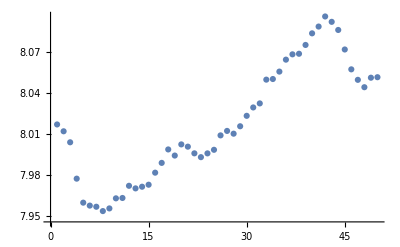

```mathematica
ListPlot[Drop[Log[output]-Table[i,{i,1,Length[output]}]*Log[1.0051],{1,218-50}]]
```

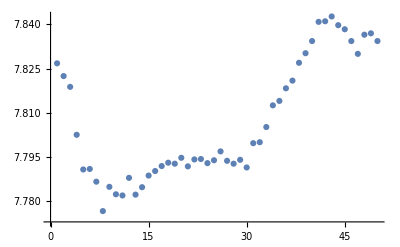

```mathematica
ListPlot[Drop[Log[consumption]-Table[i,{i,1,Length[output]}]*Log[1.0051],{1,218-50}]]
```

#### Data Treatment and Selection - End Time, Start Time. (See RBC section )

```mathematica
(*To define correctly this, we must obey the order in the RBC section Y_t=(output,hours,consumption)*)

intercept=Table[i,{i,1,Length[output]}]*Log[1.0051];

{loutput,lhours,lconsumption}={Log[output]-intercept,Log[hours],Log[consumption]-intercept};

(*
Y1Ttest=Transpose[{loutput,lhours,lconsumption}];
endTime=50;
startTime=11;
loutput=Drop[loutput,{1,Length[output]-endTime}];
lconsumption=Drop[lconsumption,{1,Length[output]-endTime}];
lhours=Drop[lhours,{1,Length[output]-endTime}];*)

Y1T=Transpose[{loutput,lhours,lconsumption}];

(*Y1T: each observation is stored in a row.*)
```

Prediction Functions

#### Initial Values

```mathematica
initValues[time_]:=Module[{X1,counter,M1,β,δ,θ,ρ,aPar,γ,A,Cmat,CmatStar,Sigma,Q,Lgp},

M1={{6.528,1.065,6.565},{1.065,1.607,0.968},{6.565,0.968,6.621}};

{β,δ,θ,ρ,aPar,γ}={0.7,0.3,0.6,0.7,2,0.6};

{A,Cmat,CmatStar}=rbcACmat[{β,δ,θ,ρ,aPar,γ}];

Sigma=DiagonalMatrix[{0.5,0.2,0.3}];

Q=DiagonalMatrix[{1.5,0.6}];

Lgp=20;

X1=ConstantArray[1,time];

X1[[1]]=RandomVariate[MultinormalDistribution[{0,0},IdentityMatrix[2]]];

counter=2;

While[counter≤time,

X1[[counter]]=A.X1[[counter-1]]+RandomVariate[MultinormalDistribution[{0,0},Q]];

counter++;
];
{X1,{M1,reparametrizationF[{β,δ,θ,ρ,aPar,γ}],reparametrizationMatern[Lgp],reparametrizationFQS[{Q,Sigma}]}}
];
```

#### Prediction 1 Step

```mathematica
prediction1Step[stateSamples_,parameterSamples_,time_,vecy1T_,sizeApproxY_,sizeBurnIn_]:=Module[{len},

len=Length[stateSamples];

(*For a Burn-In, the prediction will only use data after sizeBurnIn, i.e. sizeBurnIn+1 *)


econParSampleList=ParallelTable[reparametrizationFInv[parameterSamples[[i,2]]],{i,sizeBurnIn+1, len}];

listACCstar=ParallelTable[rbcACmat[econParSampleList[[i]]],{i,1, len-sizeBurnIn}];

listQSigma=ParallelTable[reparametrizationFQSInv[parameterSamples[[i,4]]],{i,sizeBurnIn+1, len}];


predictedState=Total[ParallelTable[listACCstar[[i-sizeBurnIn,1]].stateSamples[[i,-1]],{i,sizeBurnIn+1, len}]]/(len-sizeBurnIn);
(*This computes x_* . Computing the mean state at T+1, we must take care to use only the data after Burn-In.
*)

(*Print["1"];*)

KStarX1TList=ParallelTable[KroneckerProduct[Kint[{predictedState},stateSamples[[i]],Exp[parameterSamples[[i,3]]]],parameterSamples[[i,1]]],{i,sizeBurnIn+1,len}];
(*KStarX1TList is a list with K_M(x_*,x_{1:T}[i])\otimes M1[i] as components*)

(*Print[2];*)

KStarStarList=ParallelTable[KroneckerProduct[Kint[{predictedState},{predictedState},Exp[parameterSamples[[i,3]]]],parameterSamples[[i,1]]],{i,sizeBurnIn+1,len}];
(*KStarStarList is a list with K_M[x_*,x_* ] \otimes M1[i] as components*)

(*Print[3];*)

KX1TList=ParallelTable[KroneckerProduct[Kint[stateSamples[[i]],stateSamples[[i]],Exp[parameterSamples[[i,3]]]],parameterSamples[[i,1]]]+KroneckerProduct[IdentityMatrix[time],listQSigma[[i-sizeBurnIn,2]]],{i,sizeBurnIn+1,len}];
(*KX1TList is a list with K_M[x_{1:T}[i],x_{1:T}[i] ] \otimes M1[i] +I_T \otimes Sigma[i] as components*)

(*Print[4];*)

vecX1TList=ParallelTable[ArrayReshape[stateSamples[[i]],{Times@@Dimensions[stateSamples[[i]]],1}],{i,sizeBurnIn+1,len}];

meanDifList=ParallelTable[(vecy1T-KroneckerProduct[IdentityMatrix[time],listACCstar[[i,2]]].vecX1TList[[i]]-KroneckerProduct[ConstantArray[1,time],IdentityMatrix[3]].listACCstar[[i,3]]),{i,1,len-sizeBurnIn}];
(*meanDifList is a list with y_{1:T}-(I_T\otimes C)x_{1:T}-C_{*1:T} as components.
All the lists used to create meanDifList have length len-sizeBurnIn*)

meanbStarList=ParallelTable[listACCstar[[i,3]]+listACCstar[[i,2]].predictedState+KStarX1TList[[i]].LinearSolve[KX1TList[[i]],meanDifList[[i]]],{i,1,len-sizeBurnIn}];
(*meanbStarList gives a list with \hat\tilde b_*[i] as components.  All the lists used to create meanDifList have length len-sizeBurnIn*)

varbStarList=ParallelTable[positivizeMatrix[KStarStarList[[i]]-KStarX1TList[[i]].LinearSolve[KX1TList[[i]],Transpose[KStarX1TList⟦i⟧]]],{i,1,len-sizeBurnIn}];
(*
varbStarList is a list with \tilde Sigma_*[i] as components.
Theoretically, there should be no need for using positivizeMatrix here, however, due to machine precision considerations(rounding errors), we must ensure that it's symmetric and PD.*)

bCatList=Ceiling[RandomVariate[UniformDistribution[{0,1}],len-sizeBurnIn]*(len-sizeBurnIn)];
(*Distribution of \tilde b_* is a mixture of distributions, so we need to 'randomize', with equal prob (hence the UniformDist),  the choosing of each component distribution.*)

bStarList=ParallelTable[RandomVariate[MultinormalDistribution[Flatten[meanbStarList⟦bCatList⟦i⟧⟧],varbStarList⟦bCatList⟦i⟧⟧]],{i,1,len-sizeBurnIn}];

(*bStarList is a list of \tilde b_*[i] as components, which will be used for the approximation of the posterior predictive distribution.*)

yCatList=Ceiling[RandomVariate[UniformDistribution[{0,1}],sizeApproxY]*(len-sizeBurnIn)];
(*The posterior predictive distribution of y_* is also a mixture of distributions, so we need to 'randomize', with equal prob (hence the UniformDist),  the choosing of each component distribution.*)

yStarList=ParallelTable[RandomVariate[MultinormalDistribution[Flatten[bStarList⟦yCatList⟦i⟧⟧],listQSigma⟦yCatList⟦i⟧,2⟧]],{i,1,sizeApproxY}];
(* prediction1Step returns a sample drawn from an approximation to the posterior distribution of yStar *)

fileDataYStarList=Compress[yStarList];

(*pathname is defined below at Run Code*)
Export[pathname<>ToString[time+1]<>" - yStarList.m",fileDataYStarList];


];
```

#### Prediction N Steps

```mathematica
predictionNSteps[Y1T_,startTime_,endTime_,sizeApproxY_,sampleSize_,numParticles_, stepSize_,varSize_,sizeBurnIn_]:=Module[{},

Y1TEnd=Drop[Y1T,{1,Length[Y1T]-endTime}];
(*We drop the first Length[Y1T]-endTime obs.*)

currentTime=startTime;

While[currentTime<endTime,
(*we don't have endTime+1 observations.*)

startValues=initValues[currentTime];

(*Print["Y1T treatment"];*)
Y1TCurrent=Drop[Y1TEnd,-(endTime-currentTime)];
(*We drop the last endTime-currentTime obs*)

vecy1TCurrent=ArrayReshape[Y1TCurrent,{Times@@Dimensions[Y1TCurrent],1}];

(*Print["Y1TCurrent Dimensions = ",Dimensions[Y1TCurrent]];
Print["vecy1TCurrent Dimensions = ",Dimensions[vecy1TCurrent]];*)

(*Print["BayesianLS"];*)
{stateSamplesTime,parameterSamplesTime}=bayesianLS[currentTime,vecy1TCurrent,startValues[[2]],startValues[[1]],sampleSize,numParticles, stepSize,varSize];

(*Print["prediction1Step"];*)
prediction1Step[stateSamplesTime,parameterSamplesTime,currentTime,vecy1TCurrent,sizeApproxY,sizeBurnIn];

currentTime++;
];

];
```

Run Code for Predictions

In my simulations, I used:
startTime=10;
endTime=15;
sizeApproxY=50000;
sampleSize=15000;
numParticles=20;
stepSize=0.0001;
nuM1=15;
s1M1=1;
varSize=0.1;
sizeBurnIn=5000;

Change the below to your needs, and run the simulation.

```mathematica
pathname=NotebookDirectory[];

startTime=10;
endTime=15;
sizeApproxY=50;
sampleSize=5;
numParticles=5;
stepSize=0.0001;
nuM1=15;
s1M1=1;
varSize=0.1;
sizeBurnIn=1;
predictionNSteps[Y1T,startTime,endTime,sizeApproxY,sampleSize,numParticles, stepSize,varSize,sizeBurnIn]
```